```mathematica
hat[l_]:=Sqrt[2 l+1];
```

#### set of regulator functions to smooth the discrete result of the inverse Lorentz transfrom

```mathematica
StrengthFLorentz[E_,eps_,psiSQ_,lamM_]:=Pi^-1 psiSQ^2 eps/((E-lamM)^2+eps^2);
StrengthFLorentzTH[E_,eps_,psiSQ_,lamM_,E0_]:=(2 eps/(Pi+2 ArcTan[(lamM-E0)/eps])) psiSQ^2/((E-lamM)^2+eps^2);
StrengthFGauss[E_,eps_,psiSQ_,lamM_]:=psiSQ^2 Exp[-(E-lamM)^2/(4 eps)]/(2 Sqrt[eps Pi]);
StrengthFGaussTH[E_,eps_,psiSQ_,lamM_,E0_]:=psiSQ^2 Exp[-(E-lamM)^2/(4 eps)]/(Sqrt[eps Pi] (1+Erf[(lamM-E0)/Sqrt[4 eps]])) HeavisideTheta[E-E0];
StrengthFSinc[E_,eps_,psiSQ_,lamM_]:=(Pi (E-lamM))^-1 psiSQ^2 Sin[(E-lamM)/eps];
StrengthFBessel[E_,eps_,psiSQ_,lamM_]:=psiSQ^2 BesselJ[1/eps,(E-lamM+1)/eps]/eps;
StrengthFLaguerre[E_,eps_,psiSQ_,lamM_,nn_]:=psiSQ^2/Sqrt[Pi eps] Abs[Exp[-eps^-1 (E-lamM)^2]LaguerreL[nn,2 (E-lamM)/eps]];
```

```mathematica
Off[Inverse::luc,General::munfl,FindFit::lstol,ClebschGordan::phy]
Off[LinearSolve::luc]

ClearAll;
ImgSize=900;
workingdirectory=$HomeDirectory<>"/kette_repo/ComptonLIT/systems/mul_helion_miwchan_2/results/";(*"miwchan_inv,pitron"*)
SetDirectory[workingdirectory]
e0=ReadList["../E0.dat",Number][[1]];
hb=197.32858;
Mnucl=(938.2796+939.5731)/2.;

λi=1;λf=1; (* in/outgoing-photon polarization = ±1 ? *)
nu=0;nup=0; (* ν=0 ↔ electric multipoles *)
Ll=1;
Llp=1;
Iini=0.5;Ifin=0.5;

multipolarity=1;
parity="-";
Js={0.5};
mJs=Range[-#,#,1]&/@Js;

σI=5.;
σRmin=-10.;σRmax=100.;σRstep=1;
σRs=Range[σRmin,σRmax,σRstep];

kRange=ReadList["../kRange.dat",Number];
ks=Table[kRange[[2]]+n kRange[[3]],{n,0,kRange[[1]]-1}];
k0=0.001;k1=100;dK=0.5;
kσ=Range[k0,k1,dK];

momIndex=1;

mom=ks[[Min[momIndex,Length[ks]]]];(* to approximate Subscript[D, 1], always use the smallest momentum *)
Print["k = ",N[mom]," MeV ,   B(^3He) = ",N[e0]];
basisdims=Table[Sort[DeleteDuplicates[ToExpression[StringSplit[#,"-"][[-1]]]&/@Select[FileNames[],StringContainsQ[#,"LIT_SOURCE_"<>ToString[J]<>"^"<>parity]&]]],{J,Js}];
Print["Basis dimensions: ",basisdims]

threshold=10^-7;
nbu=6;
nBBs=Range[Min[nbu,Length[#]-1],Min[nbu+1,Length[#]]]&/@basisdims;
Print[Style["ECCE       dim_work="<>ToString[basisdims[[#]][[nBBs[[#]]]]&/@Range[Length[Js]]],12,Red]]
```

/home/kirscher/kette_repo/ComptonLIT/systems/mul_helion_miwchan_2/results

k = 0.001 MeV ,   B(^3He) = -6.034

Basis dimensions: {{42,84,119,154}}

ECCE       dim_work={{119, 154}}

#### Naive approach (pseudo-inverse solution)

JbasisDim = 119   :  ./LIT_SOURCE_0.5^-_mJ-0.5_MUL1_bv_1-119

JbasisDim = 154   :  ./LIT_SOURCE_0.5^-_mJ-0.5_MUL1_bv_1-154

JbasisDim = 119   :  ./LIT_SOURCE_0.5^-_mJ0.5_MUL1_bv_1-119

JbasisDim = 154   :  ./LIT_SOURCE_0.5^-_mJ0.5_MUL1_bv_1-154

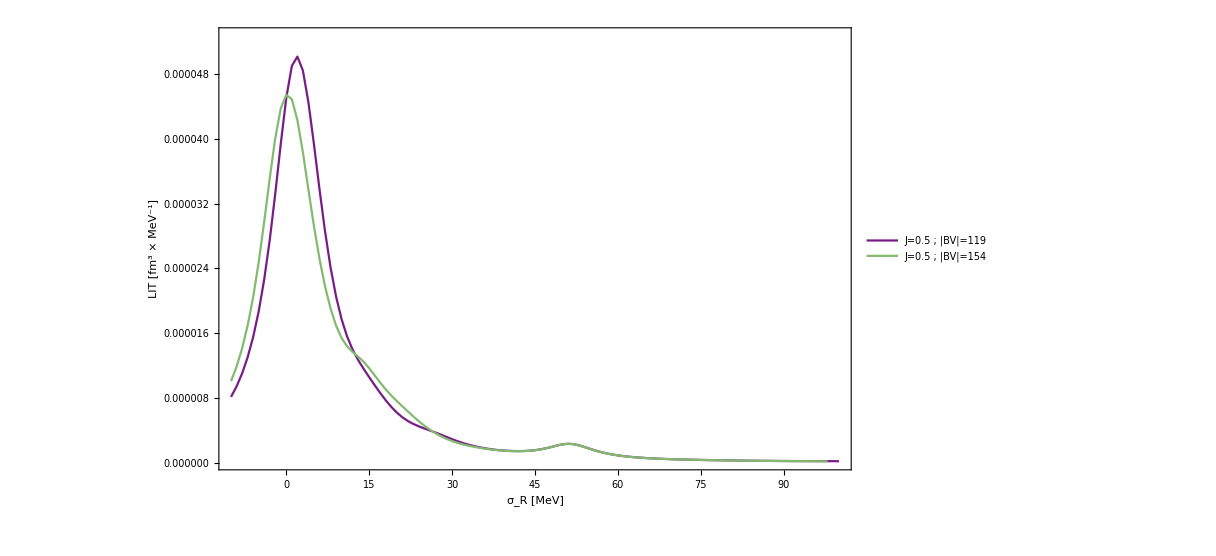

```mathematica
SetSharedVariable[LITs]
LITs={};
nJ=1;
ParallelDo[
lbd=basisdims[[nJ]][[nB]];
NormHamMat=ReadList["./norm-ham-litME-"<>ToString[Js[[nJ]]]<>"^"<>parity<>"_1-"<>ToString[lbd],Number];
JbasisDim=NormHamMat[[1]];
norm=ArrayReshape[NormHamMat[[2;;JbasisDim^2+1]],{JbasisDim,JbasisDim}];ham=ArrayReshape[NormHamMat[[JbasisDim^2+2;;2 JbasisDim^2+1]],{JbasisDim,JbasisDim}];
genevham=Sort[Eigenvalues[{ham,norm}],Re[#1]>Re[#2]&];
normev=Sort[Eigenvalues[norm],Re[#1]>Re[#2]&];
renorm=DiagonalMatrix[1/Sqrt[Diagonal[norm]]];
renormid=DiagonalMatrix[Table[1,{n,JbasisDim}]];
ham=renorm.ham.renorm;norm=renorm.norm.renorm;
genevhamN=Sort[Eigenvalues[{ham,norm}],Re[#1]>Re[#2]&];
normevN=Sort[Eigenvalues[norm],Re[#1]>Re[#2]&];

testfu=0;
Do[
file="./LIT_SOURCE_"<>ToString[Js[[nJ]]]<>"^"<>parity<>"_mJ"<>ToString[mJ]<>"_MUL"<>ToString[multipolarity]<>"_bv_1-"<>ToString[JbasisDim];
Print["JbasisDim = ",JbasisDim,"   :  ",file];
inhomo=(2/mom) ReadList[file,Real,RecordLists->True][[momIndex]];
inhomo=renorm.inhomo;
testfu+=(Function[{σR},Block[{mm,coeff},
mm=PseudoInverse[ham-(σR-σI ⅈ) norm,Tolerance->threshold];
coeff=mm.inhomo;{σR,Chop[Conjugate[coeff].norm.coeff,10^-20]}]]/@σRs)[[All,2]];
,{mJ,mJs[[nJ]][[1]],mJs[[nJ]][[-1]]}];

AppendTo[LITs,Transpose[{σRs,(-1)^(Js[[nJ]]-Iini+Ll-Llp+nup) testfu}]];

,{nB,nBBs[[nJ]]}]
pltmaxcfg=Length[LITs];
peakmax=Max[Table[Max[Re[LITs[[nn]]][[All,2]]],{nn,pltmaxcfg}]];
peakmin=Min[Table[Min[Re[LITs[[nn]]][[All,2]]],{nn,pltmaxcfg}]];
ListPlot[Re[LITs],Joined->True,Frame->True,PlotRange->{{σRs[[1]],σRs[[-1]]},{1.05 peakmin,1.05 peakmax}},FrameLabel->{Style["σ_R [MeV]",Blue,18],Style["LIT [fm^3 × MeV^-1]",Blue,18]},PlotStyle->Table[ColorData["Rainbow"][N[FractionalPart[(i-1)/(Length[LITs])]]]&[Floor[i-1,1]+1],{i,1,Length[LITs]}],PlotLegends->{"J="<>ToString[Js[[nJ]]]<>" ; |BV|="<>ToString[basisdims[[nJ]][[#]]]&/@nBBs[[nJ]]},ImageSize->ImgSize]
```

#### Alternative approach (norm zero-mode removal)

L_ν'L'νL^(I_f I_i;I_n)(k,k;σ)=(-)^(I_n-I_i+L-L'+ν')ρ(I_n,σ)∑_M_n ⟨ψ_(I_f I_i M_n)^ν'L'(k,σ)|ψ_(I_f I_i M_n)^νL(k,σ)⟩

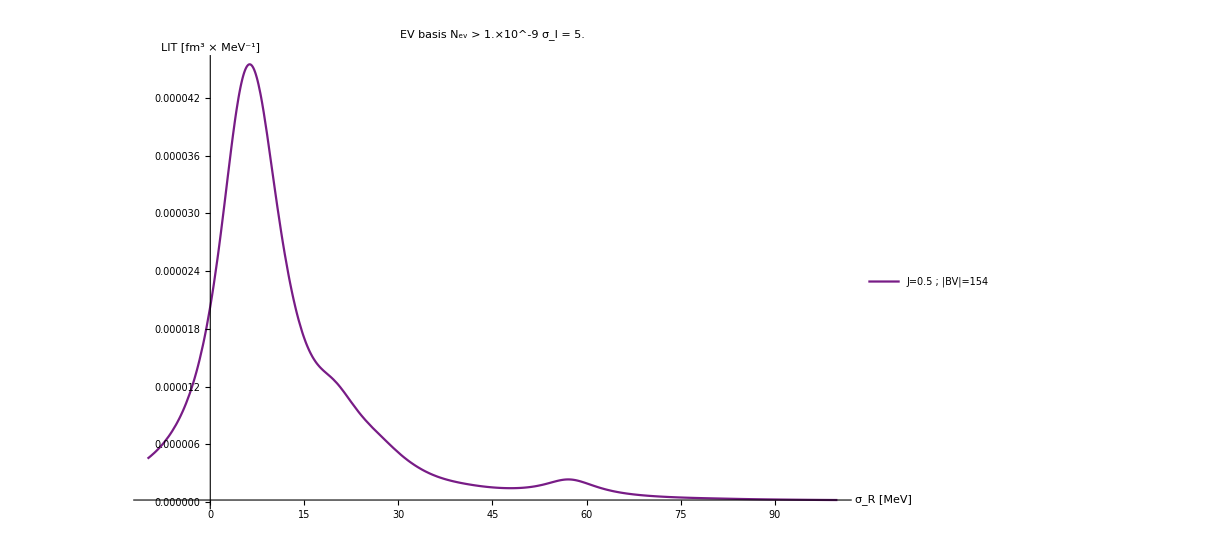

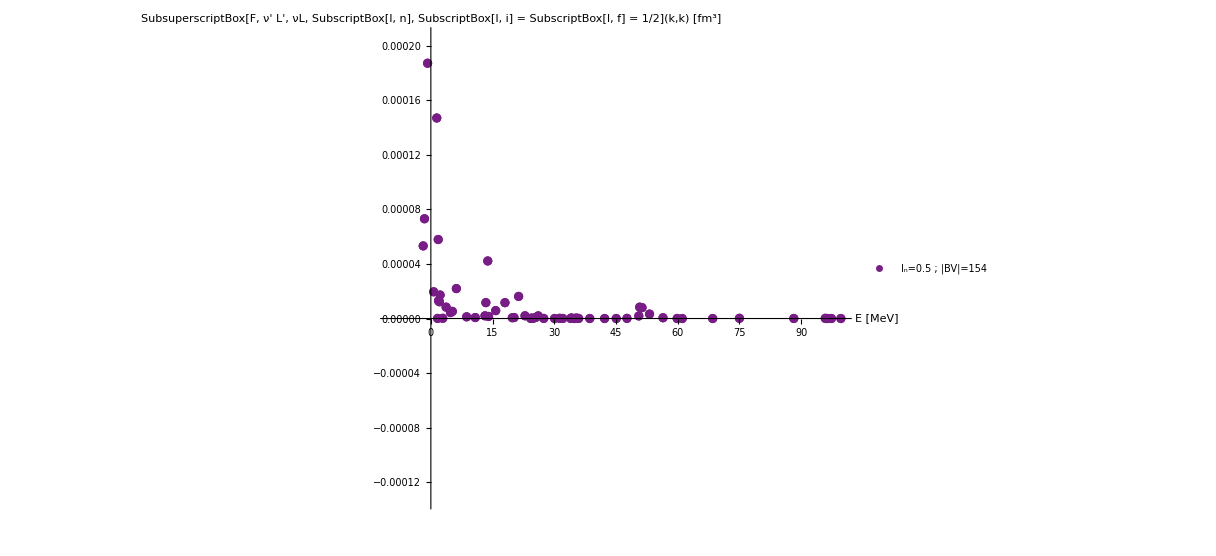

```mathematica
(*SetSharedVariable[testcompo,testfu]*)
NielsLITs={};
LITcompos={};
threshold=10^(-9);
Do[
nB=nBBs[[nJ]][[-1]];
lbd=basisdims[[nJ]][[nB]];
NormHamMat=ReadList["./norm-ham-litME-"<>ToString[Js[[nJ]]]<>"^"<>parity<>"_1-"<>ToString[lbd],Number];
JbasisDim=NormHamMat[[1]];
norm=ArrayReshape[NormHamMat[[2;;JbasisDim^2+1]],{JbasisDim,JbasisDim}];ham=ArrayReshape[NormHamMat[[JbasisDim^2+2;;2 JbasisDim^2+1]],{JbasisDim,JbasisDim}];

(*ham=ham-e0-σRe-I σI;*)

testfu=0;testcompo={};
(*---------------------------------- M sum ----------------------------------*)
Do[

file="./LIT_SOURCE_"<>ToString[Js[[nJ]]]<>"^"<>parity<>"_mJ"<>ToString[mJ]<>"_MUL"<>ToString[multipolarity]<>"_bv_1-"<>ToString[JbasisDim];
inhomo=(2/mom) ReadList[file,Real,RecordLists->True][[momIndex]];

Clear[normreg];
normreg[threshold_]:=Block[
{es=Eigensystem[norm],μ,transf,μs,Or},
{μ,transf}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]>threshold&]];
If[Dimensions[μ]<Dimensions[es[[1]]],
{μs,Or}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]<=threshold&]];
,{μs,Or}={{},{}}];
{(Transpose[transf].DiagonalMatrix[μ^(-1/2)]),Or,μs}];

Clear[decompose];
decompose[threshold_]:= Block[{Oμ,Or,μs,oλs,otrf},
{Oμ,Or,μs}=normreg[threshold];{λs,trf}=Eigensystem[(Transpose[Oμ].ham).Oμ];{λs,trf.(Transpose[Oμ].inhomo)}
];

Clear[litcomp];
litcomp[threshold_]:=Block[{λscf=Transpose[decompose[threshold]]},Plus@@((Abs[#[[2]]]^2/((#[[1]]-e0-σRe)^2+σI^2))&/@λscf)];

testfu+=Evaluate[litcomp[threshold]];

tmps=Transpose[decompose[threshold]];

testcompo=AppendTo[testcompo,Re[tmps]];
,{mJ,mJs[[nJ]][[1]],mJs[[nJ]][[-1]]}];
(*---------------------------------- M sum END ------------------------------*)
AppendTo[NielsLITs,(-1)^(Js[[nJ]]-Iini+Ll-Llp+nup) testfu];
AppendTo[LITcompos,Flatten[testcompo,1]];

,{nJ,Range[Length[Js]]}];
LITcompos=Transpose[{LITcompos[[#]][[All,1]],Re[(-1)^(Js[[#]]-Iini+Ll-Llp+nup) LITcompos[[#]][[All,2]]]}]&/@Range[Length[Js]];
Show[
Plot[NielsLITs,{σRe,-10,100},PlotRange->{Automatic,Full},
PlotLabel->"EV basis N_ev > "<>ToString[N[threshold],TraditionalForm]<>"   σ_I = "<>ToString[σI],AxesLabel->{Style["σ_R [MeV]",Blue,18],Style["LIT [fm^3 × MeV^-1]",Blue,18]},ImageSize->ImgSize,PlotStyle->Table[ColorData["Rainbow"][N[FractionalPart[(i-1)/Length[nBBs]]]]&[Floor[i-1,1]+1],{i,1,Length[nBBs]}],PlotLegends->{"J="<>ToString[Js[[#]]]<>" ; |BV|="<>ToString[basisdims[[#]][[nBBs[[#]][[-1]]]]]&/@Range[Length[Js]]},ImageSize->ImgSize]
]
maxi=1.05 Max[Table[Max[Select[LITcompos[[n]],#[[1]]<100&][[;;,2]]],{n,Length[LITcompos]}]];
mini=0.95 Min[Table[Min[Select[LITcompos[[n]],#[[1]]<100&][[;;,2]]],{n,Length[LITcompos]}]];
strengthfunctionBare=({#[[1]],(#[[2]]^2)})&/@LITcompos[[#]]&/@Range[Length[Js]];
ListPlot[strengthfunctionBare,Joined->False,PlotRange->{{-10,100},{-mini^2,maxi^2}},AxesLabel->{Style["E [MeV]",Blue,18],Style["SubsuperscriptBox[F, ν' L', νL, SubscriptBox[I, n], SubscriptBox[I, i] = SubscriptBox[I, f] = 1/2](k,k) [fm^3]",Blue,18]},PlotStyle->Table[ColorData["Rainbow"][N[FractionalPart[(i-1)/Length[Js]]]]&[Floor[i-1,1]+1],{i,1,Length[Js]}],PlotLegends->{"I_n="<>ToString[Js[[#]]]<>" ; |BV|="<>ToString[basisdims[[#]][[nBBs[[#]][[-1]]]]]&/@Range[Length[Js]]},ImageSize->ImgSize]
```

#### Alternative approach ( H→H-E_0-σ_r-i σ_i )

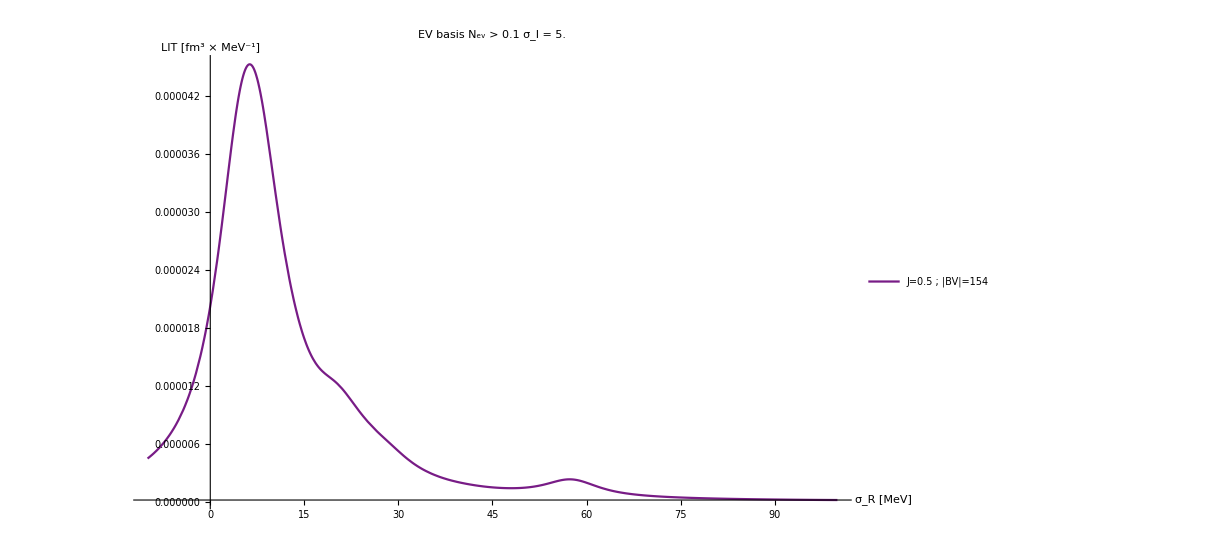

```mathematica
(*SetSharedVariable[testcompo,testfu]*)
LITs={};
LITcompos={};
threshold=10^(-1);


litti[nJ_,σRe_]:=Block[{},
nB=nBBs[[nJ]][[-1]];
lbd=basisdims[[nJ]][[nB]];
NormHamMat=ReadList["./norm-ham-litME-"<>ToString[Js[[nJ]]]<>"^"<>parity<>"_1-"<>ToString[lbd],Number];
JbasisDim=NormHamMat[[1]];
norm=ArrayReshape[NormHamMat[[2;;JbasisDim^2+1]],{JbasisDim,JbasisDim}];ham=ArrayReshape[NormHamMat[[JbasisDim^2+2;;2 JbasisDim^2+1]],{JbasisDim,JbasisDim}];
testfu=0;testcompo={};

ham=ham-norm(e0+σRe+I σI);
(*---------------------------------- M sum ----------------------------------*)
Do[

file="./LIT_SOURCE_"<>ToString[Js[[nJ]]]<>"^"<>parity<>"_mJ"<>ToString[mJ]<>"_MUL"<>ToString[multipolarity]<>"_bv_1-"<>ToString[JbasisDim];
inhomo=(2/mom) ReadList[file,Real,RecordLists->True][[momIndex]];


es=Eigensystem[norm];
{μ,transf}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]>threshold&]];

Oμ=(Transpose[transf].DiagonalMatrix[μ^(-1/2)]);

{λs,trf}=Eigensystem[(Transpose[Oμ].ham).Oμ];

λscf=Transpose[{λs,trf.(Transpose[Oμ].inhomo)}];

(*testfu+=Evaluate[Plus@@((#[[2]])^2/((#[[1]]-σRe)^2+σI^2)&/@λscf)];*)
testfu+=Evaluate[Plus@@(Abs[#[[2]]]^2/Abs[#[[1]]]^2&/@λscf)];
testcompo=AppendTo[testcompo,Re[λscf]];
,{mJ,mJs[[nJ]][[1]],mJs[[nJ]][[-1]]}];
(*---------------------------------- M sum END ------------------------------*)
{Chop[(-1)^(Js[[nJ]]-Iini+Ll-Llp+nup) testfu],Flatten[testcompo,1]}
];
(*LITcompos=Transpose[{LITcompos[[#]][[All,1]],Re[(-1)^(Js[[#]]-Iini+Ll-Llp+nup) LITcompos[[#]][[All,2]]]}]&/@Range[Length[Js]];*)
Show[
Plot[{Re[litti[1,σRe][[1]]]},{σRe,-10,100},PlotPoints->40,PlotRange->{Automatic,Full},
PlotLabel->"EV basis N_ev > "<>ToString[N[threshold],TraditionalForm]<>"   σ_I = "<>ToString[σI],AxesLabel->{Style["σ_R [MeV]",Blue,18],Style["LIT [fm^3 × MeV^-1]",Blue,18]},ImageSize->ImgSize,PlotStyle->Table[ColorData["Rainbow"][N[FractionalPart[(i-1)/Length[nBBs]]]]&[Floor[i-1,1]+1],{i,1,Length[nBBs]}],PlotLegends->{"J="<>ToString[Js[[#]]]<>" ; |BV|="<>ToString[basisdims[[#]][[nBBs[[#]][[-1]]]]]&/@Range[Length[Js]]},ImageSize->ImgSize]
]
(*maxi=1.05 Max[Table[Max[Select[LITcompos[[n]],#[[1]]<100&][[;;,2]]],{n,Length[LITcompos]}]];
mini=0.95 Min[Table[Min[Select[LITcompos[[n]],#[[1]]<100&][[;;,2]]],{n,Length[LITcompos]}]];
strengthfunctionBare=({#[[1]],(#[[2]]^2)})&/@LITcompos[[#]]&/@Range[Length[Js]];
ListPlot[strengthfunctionBare,Joined->False,PlotRange->{{-10,100},{-mini^2,maxi^2}},AxesLabel->{Style["E [MeV]",Blue,18],Style["SubsuperscriptBox[F, ν'L', νL, SubscriptBox[I, n], SubscriptBox[I, i] = SubscriptBox[I, f] = 1/2](k,k) [fm^3]",Blue,18]},PlotStyle->Table[ColorData["Rainbow"][N[FractionalPart[(i-1)/Length[Js]]]]&[Floor[i-1,1]+1],{i,1,Length[Js]}],PlotLegends->{"I_n="<>ToString[Js[[#]]]<>" ; |BV|="<>ToString[basisdims[[#]][[nBBs[[#]][[-1]]]]]&/@Range[Length[Js]]},ImageSize->ImgSize]*)
```

```mathematica
epsRange={10}(*Range[5,20,5]*);
evth=200;

responseListEL={};
responseListEG={};
Do[
responseListJ={};
For[nJ=1,nJ≤Length[Js],nJ++,
response=Total[StrengthFLorentzTH[e2,epsi,#[[2]],#[[1]],e0]&/@Select[LITcompos[[nJ]],#[[1]]<evth&]];
responseListJ=AppendTo[responseListJ,response];
];
responseListEL=AppendTo[responseListEL,responseListJ];
,{epsi,epsRange}];
responseListJ={};
Do[
For[nJ=1,nJ≤Length[Js],nJ++,
response=Total[StrengthFGaussTH[e2,epsi,#[[2]],#[[1]],e0]&/@Select[LITcompos[[nJ]],#[[1]]<evth&]];
responseListJ=AppendTo[responseListJ,response];
];
responseListEG=AppendTo[responseListEG,responseListJ];
,{epsi,epsRange}];

labeljlit2={"δ_Lorentz","δ_Gauss"};
labeljlit=("J = "<>ToString[#])&/@Js;

Plot[{responseListEL,responseListEG},{e2,-10,100},PlotRange->{{-10,100},Full},PlotLegends->Placed[labeljlit2,Bottom],PlotStyle->Table[ColorData["Rainbow"][N[FractionalPart[(i-1)/Length[Js]]]]&[Floor[i-1,1]+1],{i,1,Length[Js]}],AxesLabel->{"E [MeV]","F_j(E) [fm^3]"},PlotLabel->"ϵ ∈ "<>ToString[epsRange]<>" ; EV_th="<>ToString[evth],LabelStyle->Directive[Larger],ImageSize->ImgSize]
```

Part::partw: Part 1 of {} does not exist.

Part::partd: Part specification 1⟦1⟧ is longer than depth of object.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::partw: Part 1 of {} does not exist.

Part::partd: Part specification 1⟦1⟧ is longer than depth of object.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

-Graphics-

#### strength functions from partial strength functions

F_((ν'L'νL)J)^(I_f I_i)(k,k;E)=(E-E_0)^2∑_I_n {L
I_fL'
I_iJ
I_n} F_ν'L'νL^(I_f I_i;I_n)(k,k;E)
[fm^3·MeV^2]               [MeV^2]                                [fm^3]
i)   I_n is the total angular momentum of one element of the spectral representation of the intermediate Green function
i’) J  classifies the total angular-momentum transfer to the nucleus and assumes values  |L-L’|≤J≤|L+L’| for certain in- and out-going multi-polarities
ii) the energy-dependent prefactor is Siegert-form specific and does not appear in general!
    specifically:   ⟨ f⊗M_l|δ(Ĥ-E)|M_l'⊗i ⟩  with M_l∝1/k·[j_1(kr)Y_(1M)(Ω_r),Ĥ]

#### real and imaginary parts of the (generalized) polarizabilities from strength functions

{P_(if,J)^res(M^ν' L',M^ν L,k',k)}_imag=2 π^2 (-)^(L+I_f+I_i)L̂ L̂' [F_((ν'L'νL)J)^(I_f I_i)(k,k;E_i+k)+(-)^(L+L'+J)F_((ν'L'νL)J)^(I_f I_i)(k,k;E_i-k')]
The second term does not contribute because the initial state is the ground- and not an excited state!

ECCE: the L̂’s come from the multipole expansion of the plane wave as do the 2π’s
ImPList [I_(n=1),I_(n=2),...] [fit_1,fit_2,...] [k_0... k_max]

#### imaginary part of the amplitude and total photodisintegration cross-section

{T_(L_f λ_f;L_i λ_i)^(I_f M_f;I_i M_i)(k⃗',k⃗)}_imag=(-)^(1+λ_f+I_f-M_i) ∑_(M_L_f M_L_i J) (-)^(L_i+L_f) (L̂)^2(I_f | J | I_i
-M_f | m | M_i) (L_i | L_f | J
M_i | M_f | -m) {P_(if,J)^(L_f λ_f,L_i λ_i)(k',k)}_imag D_(M_f,-λ_f)^L_f(0,θ,0) 

ECCE: 
i)   the polarization λ affects magnetic multipole ME’s, only (see eqs. (27,29,41) )
ii)  k⃗||(e⃗)_z ⇒ D_(M,λ)^L(R)=1
iii) fm^2=10^-2 b=10mb
iv) σ(M^ν L)=(-)^(L+1)(4π)/(√(2 J_i+1)·√(2 L+1)k) ImP_0 
      from eq.(4.38) “H. Arenhoevel -- SUBNUCLEAR DEGREES OF FREEDOM IN PHOTOABSORPTION AND SCATTERING in new vistas...

```mathematica
Clear[ee,e2];
epsIndex=-1;
Ji=Jf=0.5;Mi=Ji;Mf=Mi;
Jj={0,1};
labelj=("J = "<>ToString[#])&/@Jj;
strengthfunctionListpart=Table[Table[((ee-e0)^2 responseListEL[[epsIndex]][[nJ]]/.e2->ee)/.ee->(e0+kmag),{kmag,kσ}],{nJ,Range[Length[Js]]}];
strengthfunctionList=Table[Total[Table[SixJSymbol[{Ll,Llp,Jj[[nJ]]},{Jf,Ji,Js[[nJlit]]}] strengthfunctionListpart[[nJlit,All]],{nJlit,Range[Length[Js]]}]],{nJ,Length[Jj]}];

ImPListL=2 Pi^2 (-1)^(Ll+Jf+Ji) hat[Ll] hat[Llp] strengthfunctionList;
strengthfunctionListpart=Table[Table[((ee-e0)^2 responseListEG[[epsIndex]][[nJ]]/.e2->ee)/.ee->(e0+kmag),{kmag,kσ}],{nJ,Range[Length[Js]]}];
strengthfunctionList=Table[Total[Table[SixJSymbol[{Ll,Llp,Jj[[nJ]]},{Jf,Ji,Js[[nJlit]]}] strengthfunctionListpart[[nJlit,All]],{nJlit,Range[Length[Js]]}]],{nJ,Length[Jj]}];

ImPListG=2 Pi^2 (-1)^(Ll+Jf+Ji) hat[Ll] hat[Llp] strengthfunctionList;
z=List[];

For[nJ=1,nJ≤Length[Jj],nJ++,(
atmp=ListLinePlot[ImPListL[[nJ,All]],PlotRange->Full,LabelStyle->Directive[Larger],AxesLabel->{"k [MeV]","(TraditionalForm`{SubsuperscriptBox[P, if, J, res](SuperscriptBox[M, ν'] L', SuperscriptBox[M, ν] L, k', k)})_imag [fm^3·MeV^2]"},ImageSize->ImgSize,Joined->True,DataRange->{Min[kσ],Max[kσ]},PlotStyle->{ColorData[7,"ColorList"][[nJ]]},PlotLegends->{labelj[[nJ]]}];
AppendTo[z,atmp];
atmp=ListLinePlot[ImPListG[[nJ,All]],PlotRange->Full,LabelStyle->Directive[Larger],AxesLabel->{"k [MeV]","(TraditionalForm`{SubsuperscriptBox[P, if, J, res](SuperscriptBox[M, ν'] L', SuperscriptBox[M, ν] L, k', k)})_imag [fm^3·MeV^2]"},ImageSize->ImgSize,Joined->True,DataRange->{Min[kσ],Max[kσ]},PlotStyle->{ColorData[7,"ColorList"][[nJ]]},PlotLegends->{labelj[[nJ]]}];
AppendTo[z,atmp];
)];
Show[z,PlotRange->All]

ImTL[Mf_,Mi_,λf_,λi_,θ_]:=
Module[{compo},
ampli=0;
For[nJ=1,nJ≤Length[Jj],nJ++,(
compo=hat[Jj[[nJ]]]^2 ImPListL[[nJ,All]];
For[Mm=-Ll,Mm≤Ll,Mm++,(
For[Mmp=-Llp,Mmp≤Llp,Mmp++,
(
ampli+=ThreeJSymbol[{Jf,-Mf},{Jj[[nJ]],Mf-Mi},{Ji,Mi}] ThreeJSymbol[{Ll,Mm},{Llp,Mmp},{Jj[[nJ]],-Mm-Mmp}] WignerD[{Llp,Mmp,-λf},0,θ,0] compo;
)];)];)];
Return[(-1)^(1+λf+Jf-Mi)*ampli]
]

ImTG[Mf_,Mi_,λf_,λi_,θ_]:=
Module[{compo},
ampli=0;
For[nJ=1,nJ≤Length[Jj],nJ++,(
compo=hat[Jj[[nJ]]]^2 ImPListG[[nJ,All]];
For[Mm=-Ll,Mm≤Ll,Mm++,(
For[Mmp=-Llp,Mmp≤Llp,Mmp++,
(
ampli+=ThreeJSymbol[{Jf,-Mf},{Jj[[nJ]],Mf-Mi},{Ji,Mi}] ThreeJSymbol[{Ll,Mm},{Llp,Mmp},{Jj[[nJ]],-Mm-Mmp}] WignerD[{Llp,Mmp,-λf},0,θ,0] compo;
)];)];)];
Return[(-1)^(1+λf+Jf-Mi)*ampli]
]

kinfac=-(4 Pi)/(137  √6 kσ);

DissCrossL[Mf_,Mi_,λf_,λi_,θ_,kinfac_]:=kinfac ImTL[Mf,Mi,λf,λi,θ];
DissCrossG[Mf_,Mi_,λf_,λi_,θ_,kinfac_]:=kinfac ImTG[Mf,Mi,λf,λi,θ];

ListPlot[{Re[DissCrossL[Jf,Ji,1,0,0,kinfac]],Re[DissCrossG[Jf,Ji,1,0,0,kinfac]]},PlotRange->Full,LabelStyle->Directive[Larger],AxesLabel->{"k [MeV]","(TraditionalForm`-FractionBox[(4  π) α , SqrtBox[6] k] {SubsuperscriptBox[T, λ' λ, fi](OverscriptBox[k, ⇀]', OverscriptBox[k, ⇀])})_imag [mb]"}(*,Filling->cycl*),ImageSize->ImgSize,Joined->True,DataRange->{Min[kσ],Max[kσ]},PlotLegends->{"δ_Lorentz","δ_Gauss"}]
```

-Graphics-

-Graphics-

```mathematica
nJ=1;
JbasisDim=basisdims[[nJ]][[1;;]];
file="./LIT_SOURCE_"<>ToString[Js[[nJ]]]<>"^"<>parity<>"_mJ"<>ToString[mJs[[nJ]][[2]]]<>"_MUL"<>ToString[multipolarity]<>"_bv_1-"<>ToString[#]&/@JbasisDim;
Print["JbasisDim = ",JbasisDim];

inhomo=(*(2/mom)*) (ReadList[#,Real,RecordLists->True]&/@file)[[-1]][[1;;1]];
inhomomeans=Mean[#]&/@inhomo;
minhomo=Table[inhomomeans[[#]],{n,Length[inhomo[[#]]]}]&/@Range[Length[inhomo]];
Show[ListPlot[inhomo,Joined->True,PlotRange->Full,ImageSize->ImgSize,PlotLabels->Range[Length[inhomo]]],
ListPlot[minhomo,Joined->True,PlotRange->Full,ImageSize->ImgSize,PlotStyle->{Dashed,Opacity[0.5]}]]
```

JbasisDim = {42,84,119,154}

-Graphics-

JbasisDim = {42,84,119,154}

Transpose::nmtx: The first two levels of {} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

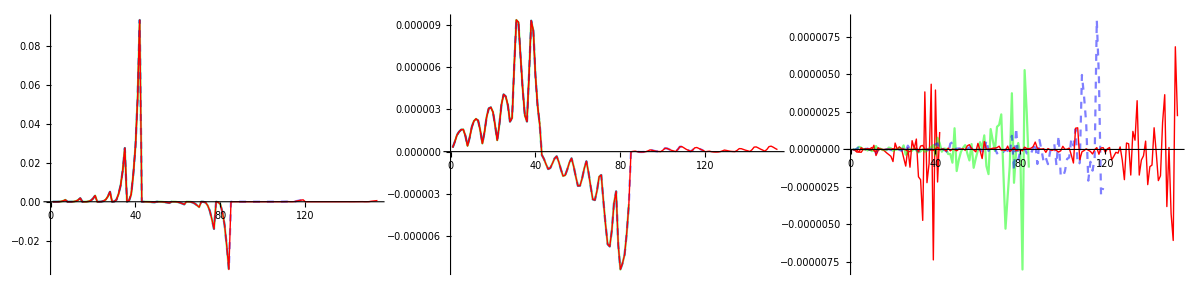

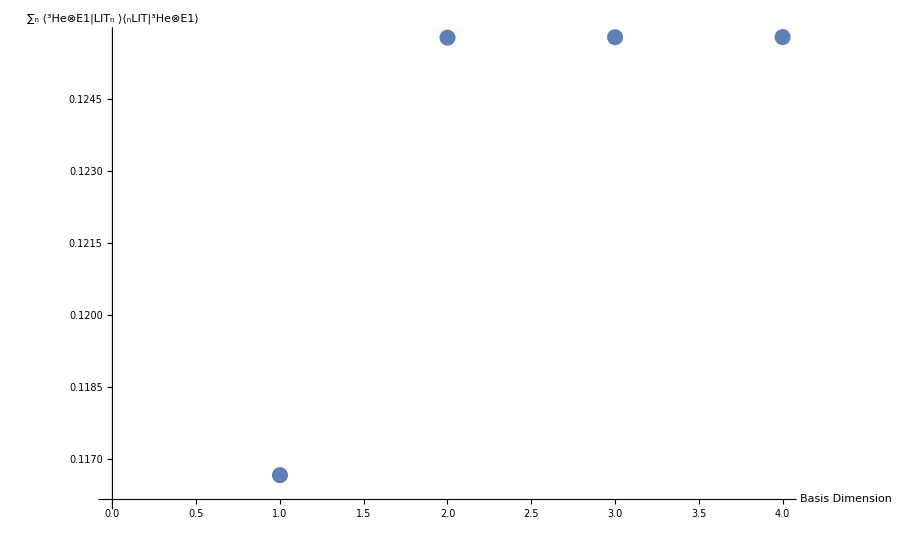

```mathematica
nJ=1;
momIndex=1;
threshold=10^(-12);
lbd=basisdims[[nJ]];
NormHamMat=ReadList["./norm-ham-litME-"<>ToString[Js[[nJ]]]<>"^"<>parity<>"_1-"<>ToString[#],Number]&/@lbd;
JbasisDim=NormHamMat[[All,1]];
norm=ArrayReshape[#[[2;;#[[1]]^2+1]],{#[[1]],#[[1]]}]&/@NormHamMat;
ham=ArrayReshape[#[[#[[1]]^2+2;;2 #[[1]]^2+1]],{#[[1]],#[[1]]}]&/@NormHamMat;
genevham=Sort[Eigenvalues[{ham[[#]],norm[[#]]}],Re[#1]>Re[#2]&]&/@Range[Length[JbasisDim]];
normev=Sort[Eigenvalues[#],Re[#1]>Re[#2]&]&/@norm;
file="./LIT_SOURCE_"<>ToString[Js[[nJ]]]<>"^"<>parity<>"_mJ"<>ToString[mJs[[nJ]][[1]]]<>"_MUL"<>ToString[multipolarity]<>"_bv_1-"<>ToString[#]&/@JbasisDim;
Print["JbasisDim = ",JbasisDim];


inhomo=(*(2/mom)*) ReadList[#,Real,RecordLists->True][[momIndex]]&/@file;

renorm=DiagonalMatrix[1/Sqrt[Diagonal[#]]]&/@norm;
renormid=DiagonalMatrix[Table[1,{n,#}]]&/@JbasisDim;
hamre=renorm[[#]].ham[[#]].renorm[[#]]&/@Range[Length[JbasisDim]];

normre=renorm[[#]].norm[[#]].renorm[[#]]&/@Range[Length[JbasisDim]];
inhomore=renorm[[#]].inhomo[[#]]&/@Range[Length[JbasisDim]];
genevhamN=Eigenvalues[{hamre[[#]],normre[[#]]}]&/@Range[Length[JbasisDim]];
normevN=Sort[Eigenvalues[#],Re[#1]>Re[#2]&]&/@normre;

es=Eigensystem[norm[[#]]]&/@Range[Length[JbasisDim]];
μtransf=Transpose[Select[Sort[Transpose[es[[#]]],#1[[1]]<#2[[1]]&],#1[[1]]>threshold&]]&/@Range[Length[JbasisDim]];
μsOr=Transpose[Select[Sort[Transpose[es[[#]]],#1[[1]]<#2[[1]]&],#1[[1]]<=threshold&]]&/@Range[Length[JbasisDim]];
Oμ=(Transpose[μtransf[[#]][[2]]].DiagonalMatrix[(μtransf[[#]][[1]])^(-1/2)])&/@Range[Length[JbasisDim]];
λstrf=Eigensystem[(Transpose[Oμ[[#]]].ham[[#]]).Oμ[[#]]]&/@Range[Length[JbasisDim]];
inhomoCl=λstrf[[#]][[2]].(Transpose[Oμ[[#]]].inhomo[[#]])&/@Range[Length[JbasisDim]];

Grid[{{ListPlot[inhomo,Joined->True,PlotRange->Full,ImageSize->ImgSize,PlotStyle->{{Thick,Red},{Green,Opacity[0.5]},{Blue,Dashed,Opacity[0.5]}}],ListPlot[inhomore,Joined->True,PlotRange->Full,ImageSize->ImgSize,PlotStyle->{{Thick,Red},{Green,Opacity[0.5]},{Blue,Dashed,Opacity[0.5]}}],
ListPlot[inhomoCl,Joined->True,PlotRange->Full,ImageSize->ImgSize,PlotStyle->{{Thick,Red},{Green,Opacity[0.5]},{Blue,Dashed,Opacity[0.5]}}]}}]
norminhom=Norm[inhomo[[#]]]&/@Range[Length[JbasisDim]];
ListPlot[norminhom,AxesLabel->{Style["Basis Dimension",Large],Style["∑_n ⟨^3He⊗E1|LIT_n ⟩⟨_nLIT|^3He⊗E1⟩",Large]},ImageSize->900]
```

#### regulator normalization

∫∞/E_0 dE e^(-β·E^2)=

```mathematica
(*Integrate[Exp[-β (e-λ)^2],{e,Subscript[E, 0],Infinity},Assumptions->{β>0}]*)
```

```mathematica
eps=21.;
2 Sqrt[eps Pi]
(Sqrt[eps Pi] Erfc[e0/Sqrt[4 eps]])
```

16.2448

13.3872

```mathematica
(*Integrate[1/((e-sr)^2+si),{e,Subscript[E, 0],Infinity},Assumptions->{si>0,sr>0}]*)
```

```mathematica
ArcTan[Infinity]
```

π/2